# -Graphics-

# Finite Element Programming with the Wolfram Language Part: 2

-Graphics--Graphics-

## M. K. AbdElrahman

## Wolfram Research

## Last Time

### Introduction

### Finite Element Data within NDSolve

### Passing Finite Element Options to NDSolve

### A Workflow Overview

### The Partial Differential Equation Problem Setup

### Stationary PDEs

## Last Time

```mathematica
Needs["NDSolve`FEM`"]
```

Define Region:

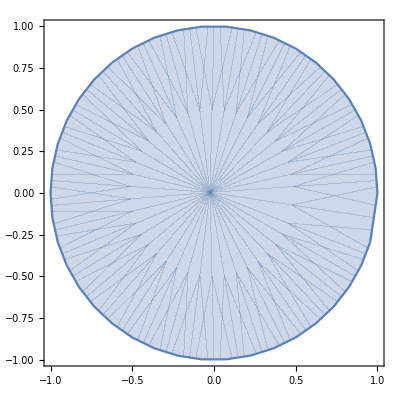

```mathematica
Ω= Disk[];
Show[RegionPlot[Ω]]
```

Define  PDE:

```mathematica
Epsilon[x_,y_]:= 1+x^2+y^2
pde = PoissonPDEComponent[{u[x,y],{x,y}},<|"PoissonSourceTerm"->Epsilon[x,y]|>]==0
Subscript[Γ, D]= {DirichletCondition[u[x,y]==0.0,True]};
```

-1-x^2-y^2+({{1,0},{0,1}}.u[x,y]{x,y}Inactive){x,y}Inactive==0

ProcessEquation:

```mathematica
{dpde,dbc,vd,sd,mdata}=ProcessPDEEquations[{pde,Subscript[Γ, D]},u,{x,y}∈Ω];
```

Discretize PDE

```mathematica
{load,stiffness,damping,mass}=dpde["All"];
```

Discretize the  boundary conditions.

```mathematica
DeployBoundaryConditions[{load,stiffness},dbc];
```

Linear Solve

```mathematica
solution = LinearSolve[stiffness,load];
```

Save Solution

```mathematica
NDSolve`SetSolutionDataComponent[sd,"DependentVariables",Flatten[solution]];
```

Create an InterpolatingFunctionpaclet:ref/InterpolatingFunction object.

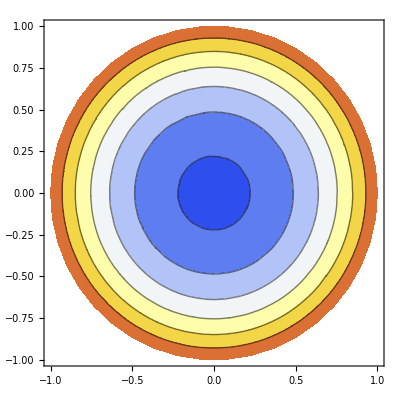

```mathematica
mesh = mdata["ElementMesh"];
ifun=ElementMeshInterpolation[mesh, solution];
ContourPlot[ifun[x,y],{x,y}∈Ω,PlotRange->All,ColorFunction->"TemperatureMap"]
```

## Outline

### Transient PDEs

### Finite Element Method addons for Wolfram Language

### Element Mesh Generation

### Element Mesh Visualization

### Examples

## Transient PDEs

The first example is a heat equation in 1D. Consider the following model PDE

∂/(∂t)u+∇·(- ∇u)=1

in a spatial region from 0 to 1 and a time domain from 0 to 1. Boundary and initial conditions are 0 everywhere:

```mathematica
<<NDSolve`FEM`
```

```mathematica
ufun=NDSolveValue[{D[u[t,x],{t,1}]-D[u[t,x],{x,2}]==1,u[0,x]==0,DirichletCondition[u[t,x]==0,True]},u,{t,0,1},{x,0,1},
Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement"}}}]
```

InterpolatingFunction[…]

Plot the numerical solution:

```mathematica
Plot3D[ufun[t,x],{t,0,1},{x,0,1}]
```

-Graphics3D-

First, the variable data is created and populated:

```mathematica
vd=NDSolve`VariableData[{"DependentVariables"->{u},"Space"->{x},"Time"->t}]
```

{t,{x},{u},{},{},{},{},{}}

Specify a NumericalRegion:

```mathematica
nr=ToNumericalRegion[FullRegion[1],{{0,1}}]
```

NumericalRegion[FullRegion[1],{{0,1}}]

Create the solution data with the "Space" and "Time" components set:

```mathematica
sd=NDSolve`SolutionData[{"Space"->nr,"Time"->0.}]
```

{0.,NumericalRegion[FullRegion[1],{{0,1}}],{},{},{},{},{},{}}

Initialize the partial differential equation coefficients:

```mathematica
initCoeffs=InitializePDECoefficients[vd,sd,"DiffusionCoefficients"->
{{-IdentityMatrix[1]}},"LoadCoefficients"->{{1}},"DampingCoefficients"->{{1}}]
```

PDECoefficientData[<1,1>]

Initialize the boundary conditions:

```mathematica
initBCs=InitializeBoundaryConditions[vd,sd,{{DirichletCondition[u[t,x]==0,True]}}]
```

BoundaryConditionData[<1,1>]

Initialize the finite element data with the variable and solution data:

```mathematica
methodData=InitializePDEMethodData[vd,sd]
```

FEMMethodData[<41,{2},4>]

Extract the ElementMesh from the NumericalRegion:

```mathematica
mesh=nr["ElementMesh"]
```

ElementMesh[{{0.,1.}},{LineElement[<20>]}]

Compute the discretized partial differential equation:

```mathematica
discretePDE=DiscretizePDE[initCoeffs,methodData,sd]
```

DiscretizedPDEData[<41>]

Discretize the initialized boundary conditions:

```mathematica
discreteBCs=DiscretizeBoundaryConditions[initBCs,methodData,sd]
```

DiscretizedBoundaryConditionData[<41>]

Extract all system matrices:

```mathematica
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"];
```

Deploy the boundary conditions in place:

```mathematica
DeployBoundaryConditions[{load,stiffness,damping},discreteBCs]
```

DeployedBoundaryConditionData[<Insert>]

Set up initial conditions based on the boundary conditions:

```mathematica
init=Table[{0.},{methodData["DegreesOfFreedom"]}];
init[[discreteBCs["DirichletRows"]]]=discreteBCs["DirichletValues"];
```

Time-integrate the system of equations with NDSolve:

```mathematica
tufun=NDSolveValue[{damping.u'[ t]+stiffness.u[ t]==load,u[0]==init},u,{t,0,1},
Method->{"TimeIntegration"->"IDA"},AccuracyGoal->$MachinePrecision/4,PrecisionGoal->$MachinePrecision/4]
```

InterpolatingFunction[…]

Set up a function that, given a time t, constructs and memorizes an interpolating function:

```mathematica
ClearAll[fun]
fun[t_?NumericQ]:=fun[t]=ElementMeshInterpolation[{mesh}, tufun[t]]
```

Visualize the difference between the automatic and manual solutions:

```mathematica
Plot3D[fun[t][x]-ufun[t,x],{t,0,1},{x,0,1}]
```

-Graphics3D-

## Finite Element Method addons for Wolfram Language

The easiest way to install or update the FEMAddOns is to evaluate the following:

```mathematica
ResourceFunction["FEMAddOnsInstall"][]
```

PacletObject[…]

```mathematica
PacletInstall["/home/mk/Downloads/FEMAddOns-1.4.5.paclet"]
```

PacletObject[…]

```mathematica
PacletFind["FEMAddOns"]
```

{}

```mathematica
PacletUninstall["FEMAddOns"]
```

For example generate structured meshes with StructuredMesh:

```mathematica
Needs["FEMAddOns`"]
```

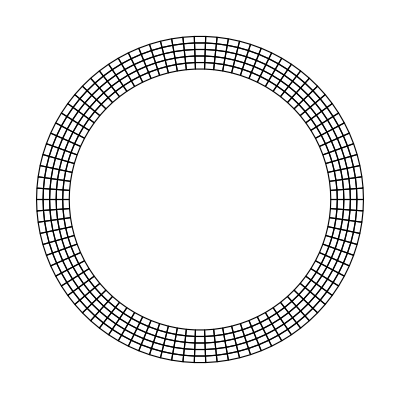

```mathematica
raster = Table[#, {fi, 0, 2 Pi, 2.0 Pi/360}] & /@ {{Cos[fi], Sin[fi]}, 0.8*{Cos[fi], Sin[fi]}};
mesh = StructuredMesh[raster, {90, 5}];
mesh["Wireframe"]
```

With ToQuadMesh convert triangle meshes into quadrilateral meshes:

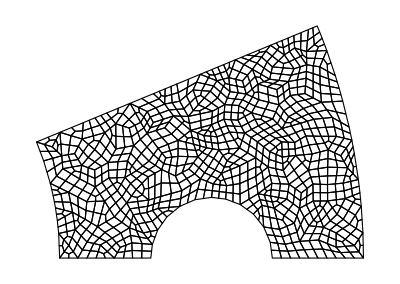

```mathematica
region = ImplicitRegion[And @@ (# <= 0 & /@ {-y, 1/25 - (-3/2 + x)^2 - y^2, 
   1 - x^2 - y^2, -4 + x^2 + y^2, y - x*Tan[Pi/8]}), {x, y}];
ToQuadMesh[ToElementMesh[region]]["Wireframe"]
```

Use the DistMesh mesh generator to create smooth meshes:

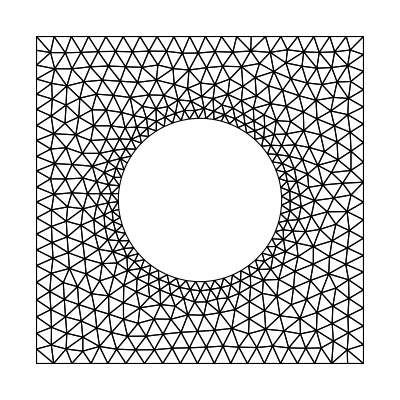

```mathematica
mesh = DistMesh[RegionDifference[Rectangle[{-1, -1}, {1, 1}], Disk[{0, 0}, 1/2]], 
   "DistMeshRefinementFunction" -> 
    Function[{x, y}, Min[4*Sqrt[Plus @@ ({x, y}^2)] - 1, 2]], 
   "MaxCellMeasure" -> {"Length" -> 0.05}, 
   "IncludePoints" -> {{-1, -1}, {-1, 1}, {1, -1}, {1, 1}}]; 
mesh["Wireframe"]
```

With ImportMesh load meshes from Abaqus, Comsol, Elfen and Gmsh

```mathematica
mesh = ImportMesh[ "filePath", "mesh.mphtxt"];
mesh["Wireframe"]
```

ImportMesh[filePath,mesh.mphtxt][Wireframe]

## Element Mesh Generation

#### Passing an ElementMesh to NDSolve

Set up a region:

```mathematica
Ω=ImplicitRegion[True,{{x,0,2},{y,0,1}}]
```

ImplicitRegion[0≤x≤2&&0≤y≤1,{x,y}]

Set up a PDE operator:

```mathematica
op=-Laplacian[u[x,y],{x,y}]-20
```

-20-u^(0,2)[x,y]-u^(2,0)[x,y]

Specify boundary conditions:

```mathematica
Γ=DirichletCondition[u[x,y]==0, x==0||x==2]
```

DirichletCondition[u[x,y]==0,x==0||x==2]

Solve the PDE:

```mathematica
ufun=NDSolveValue[{op==0,Γ},u,{x,y}∈Ω]
```

InterpolatingFunction[…]

Plot a contour plot of the solution with the element mesh from the interpolation function on top:

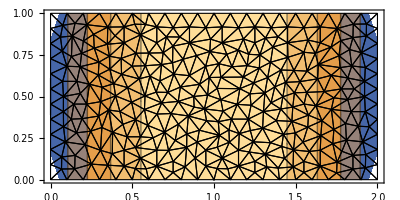

```mathematica
Show[
ContourPlot[ufun[x,y],{x,y}∈Ω,AspectRatio->Automatic],
ufun["ElementMesh"]["Wireframe"]]
```

Extract the ElementMesh from an interpolating function:

```mathematica
ufun["ElementMesh"]
```

Instead of specifying an implicit parametric region, it is also possible to specify an explicit ElementMesh. This can be done by using ToElementMesh:

```mathematica
mesh=ToElementMesh["Coordinates"->{{0.,0.},{1.,0.},{2.,0.},{2.,1.},{1.,1.},{0.,1.}},
"MeshElements"->{TriangleElement[{{1,2,5},{5,6,1},{2,3,4},{4,5,2}}]}]
```

ElementMesh[{{0.,2.},{0.,1.}},{TriangleElement[<4>]}]

Show a wireframe of the element mesh:

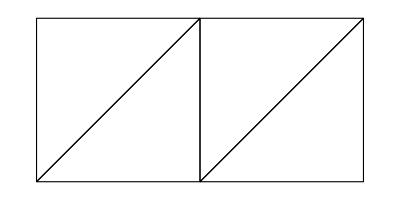

```mathematica
mesh["Wireframe"]
```

Next, the same PDE is solved, this time with only the explicit mesh defined:

```mathematica
ufun=NDSolveValue[{op==0,Γ},u[x,y],{x,y}∈mesh];
```

This makes a contour plot of the solution and plots the element mesh:

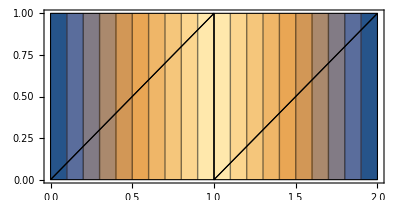

```mathematica
Show[
ContourPlot[ufun,{x,y}∈mesh,AspectRatio->Automatic],
mesh["Wireframe"]]
```

## Element Mesh Generation

#### Passing Options for the ElementMesh Creation to NDSolve via MeshOptions

Solve the PDE with options given to influence the element mesh generation:

```mathematica
ufun=NDSolveValue[{op==0,Γ},u,{x,y}∈Ω,Method->{"FiniteElement","MeshOptions"->{MaxCellMeasure->0.01}}]
```

InterpolatingFunction[…]

As an alternative, the element mesh can be generated prior to the simulation and given to NDSolve:

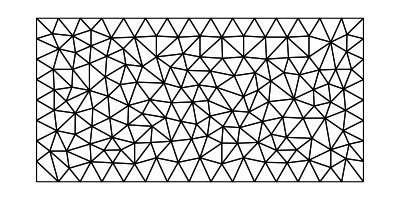

```mathematica
mesh=ToElementMesh[Ω,MaxCellMeasure->0.01];
mesh["Wireframe"]
```

```mathematica
ufun=NDSolveValue[{op==0,Γ},u,{x,y}∈mesh]
```

InterpolatingFunction[…]

Solve the time-dependent PDE with options given to influence the element mesh generation:

```mathematica
ufun=NDSolveValue[{D[u[t,x,y],t]-Laplacian[u[t,x,y],{x,y}]-20==0,DirichletCondition[u[t,x,y]==0, x==0||x==2],u[0,x,y]==0},u,{t,0,1},{x,y}∈Ω,
Method->{"PDEDiscretization"->{Automatic,"SpatialDiscretization"->{"FiniteElement","MeshOptions"->{MaxCellMeasure->0.01}}}}]
```

InterpolatingFunction[{{0., 1.}, {0., 2.}, {0., 1.}}, <>]

## Element Mesh Generation

#### Element Meshes with Subregions

It is common for a PDE to interact with a region that is made up of multiple materials. The solutions of PDEs will be of a higher quality if the mesh elements do not cross the internal boundaries. To illustrate this, a PDE with a variable diffusion coefficient is reconsidered and solved over two regions (see Solving Partial Differential Equations with Finite Elements). One region respects the internal boundary, while the other does not:

```mathematica
sh=0.2;sh2=0.02;sw=0.3;
coordinates={{0.,0.},{1.,0.},{1.,sh},{1.,1.},{0.,1.}, {0.,sh+sh2}, {sw,sh+sh2},{sw,sh},{0.,sh}};
el1=LineElement[{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,1}}];
bMesh1=ToBoundaryMesh["Coordinates"->coordinates, "BoundaryElements"->{el1,LineElement[{{3,8}}]}];
bMesh2=ToBoundaryMesh["Coordinates"->coordinates, "BoundaryElements"->{el1}];
GraphicsRow[{bMesh1["Wireframe"],bMesh2["Wireframe"]}]
```

-Graphics-

The diffusion coefficient has a jump discontinuity at y=0.2. Set up a diffusion coefficient that is space dependent:

```mathematica
ϵr=If[y≤sh,{{11.7,0.},{0.,11.7}},{{1.,0},{0.,1.}}]
```

If[y≤0.2,{{11.7,0.},{0.,11.7}},{{1.,0},{0.,1.}}]

Create and visualize the element meshes:

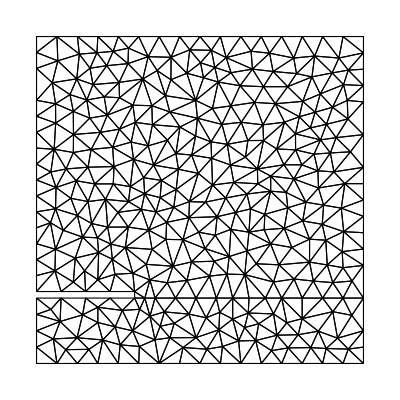
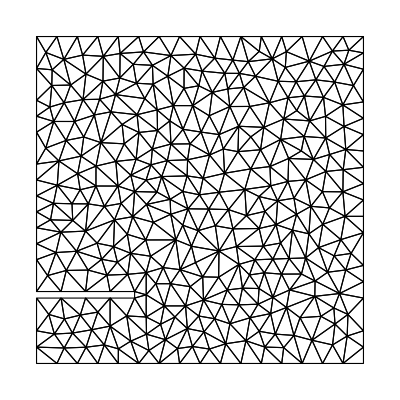

```mathematica
mesh1=ToElementMesh[bMesh1];
mesh2=ToElementMesh[bMesh2];
{mesh1["Wireframe"],mesh2["Wireframe"]}
```

Specify a PDE operator and boundary conditions:

```mathematica
op=Inactive[Div][-ϵr.Inactive[Grad][u[x,y],{x,y}],{x,y}]-10^-8./8.86*^-12;
Subscript[Γ, D]={DirichletCondition[u[x,y]==0,x==1||y==1||y==0],
DirichletCondition[u[x,y]==10^3,0<x≤sw&&sh≤y≤sh+sh2]};
```

Solve the equation over each mesh:

```mathematica
ufun1=NDSolveValue[{op==0,Subscript[Γ, D]},u,{x,y}∈mesh1];
```

```mathematica
ufun2=NDSolveValue[{op==0,Subscript[Γ, D]},u,{x,y}∈mesh2];
```

Visualize the solution:

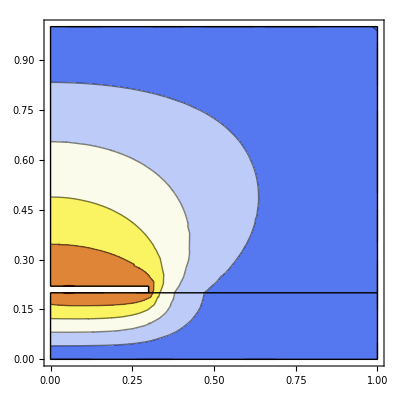
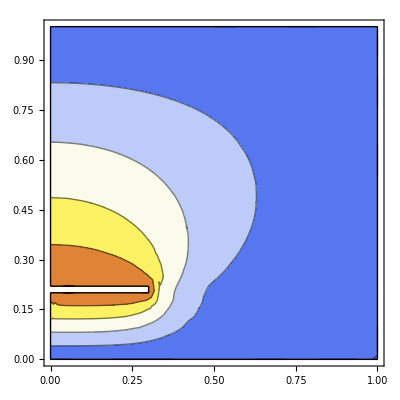

```mathematica
{
Show[ContourPlot[ufun1[x,y],{x,y}∈mesh1,ColorFunction->"TemperatureMap",AspectRatio->Automatic],
bMesh1["Wireframe"]],
Show[ContourPlot[ufun2[x,y],{x,y}∈mesh2,ColorFunction->"TemperatureMap",AspectRatio->Automatic],
bMesh2["Wireframe"]]
}
```

Visualize the difference between the two solutions:

```mathematica
Plot3D[ufun1[x,y]-ufun2[x,y],{x,y}∈mesh1,ColorFunction->"TemperatureMap",PlotRange->All,Boxed->False]
```

-Graphics3D-

The next example shows a circular region with a subregion and holes inside the subregion:

```mathematica
annulus[x_,y_]:=(9/10)^2≤x^2+y^2≤1^2
holes[{x0_,y0_},r_]:=((x+x0)^2+(y+y0)^2≤(r)^2)
crds={{-1/2,0},{1/2,0},{0,-1/2},{0,1/2},{2/5,2/5},{-2/5,-2/5},{2/5,-2/5},{-2/5,2/5}};
sd=Or@@(holes[#,1/8]&/@crds);
```

Display the region:

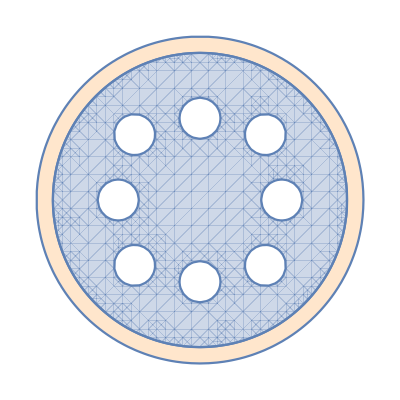

```mathematica
Show[
RegionPlot[annulus[x,y],{x,-1,1},{y,-1,1},PlotStyle->LightOrange],
RegionPlot[x^2+y^2<(9/10)^2&&!sd,{x,-1,1},{y,-1,1}]
,Frame->False]
```

Specify the region as an implicit region and create an element mesh:

```mathematica
Ω2=ImplicitRegion[Or[annulus[x,y],sd],{x,y}];
ToElementMesh[Ω2][“Wireframe”]
```

ElementMesh[{{-1.,1.},{-1.,1.}},{TriangleElement[<320>]}][CurlyDoubleQuote[Wireframe]]

In the next step, what is a region hole and what is not is inverted in the subregion by explicitly specifying the region holes:

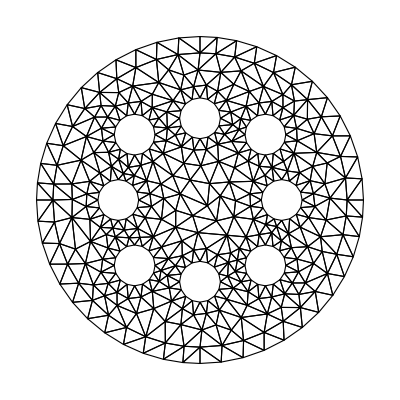

```mathematica
ToElementMesh[Ω2,"RegionHoles"->crds]["Wireframe"]
```

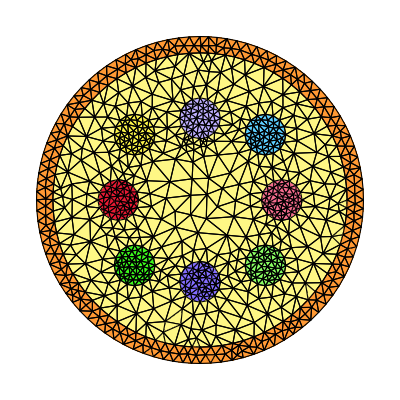

```mathematica
mesh=ToElementMesh[Ω2,"RegionHoles"->None,"RegionMarker"->Join[
MapThread[{#1,#2,0.001}&,{crds,Range[Length[crds]]}],{{{0,0},Length[crds]+1,0.01},{{19/20,0},Length[crds]+2,0.002}}]];
temp=Most[Range[0,1,1/(Length[crds]+2)]];
colors=ColorData["BrightBands"][#]&/@temp;
mesh["Wireframe"["MeshElementStyle"->FaceForm/@colors]]
```

## Element Mesh Visualization

An ElementMesh is typically created with either ToBoundaryMesh or ToElementMesh:

```mathematica
Needs["NDSolve`FEM`"]
```

Create a triangle element mesh with six triangle elements and markers:

```mathematica
mesh=ToElementMesh["Coordinates"->{{1.293,0.228},{1.,0.},{0.94,0.342},{1.293,0.},{1.215,0.442},{2.,0.},{1.879,0.684}},
"MeshElements"-> {TriangleElement[{{1,3,2},{1,2,4},{1,4,6},{1,6,7},{1,7,5},{1,5,3}},{66,66,66,44,44,44}]}]
```

ElementMesh[{{0.94,2.},{0.,0.684}},{TriangleElement[<6>]}]

Visualize the element mesh wireframe:

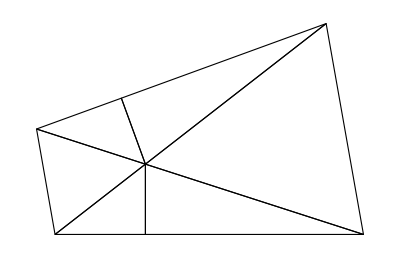

```mathematica
mesh["Wireframe"]
```

Convert to a MeshRegion:

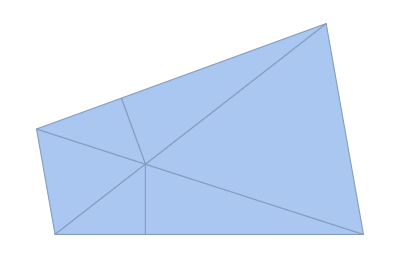

```mathematica
MeshRegion[mesh]
```

Visualize the element mesh wireframe in green:

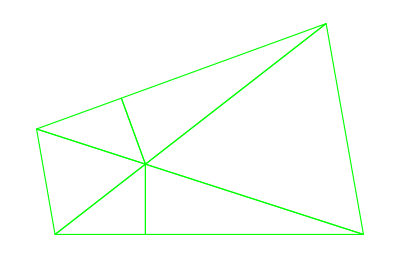

```mathematica
mesh["Wireframe"["MeshElementStyle"->EdgeForm[Green]]]
```

Visualize the element mesh in green:

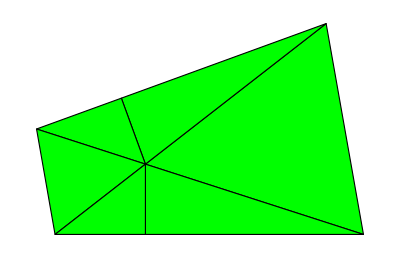

```mathematica
mesh["Wireframe"["MeshElementStyle"->FaceForm[Green]]]
```

Visualize the element mesh in green and the faces in red:

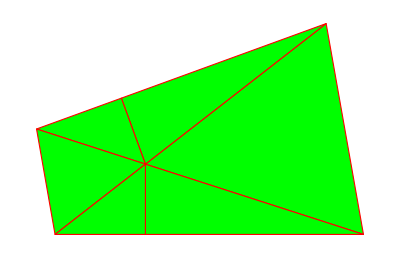

```mathematica
mesh["Wireframe"["MeshElementStyle"->Directive[FaceForm[Green],EdgeForm[Red]]]]
```

Visualize the element mesh wireframe with the element identification numbers in red:

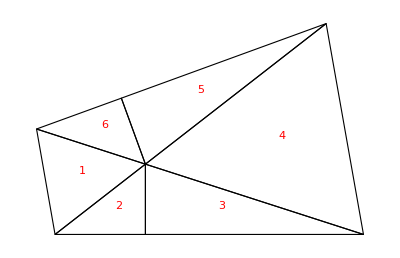

```mathematica
mesh["Wireframe"["MeshElementIDStyle"->Red]]
```

Visualize the element mesh wireframe with the element markers in blue:

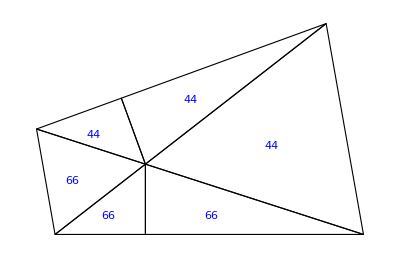

```mathematica
mesh["Wireframe"["MeshElementMarkerStyle"->Blue]]
```

Find the positions of elements that have a quality less than 0.9:

```mathematica
pos=Position[mesh["Quality"],_?(#≤0.9&)]
```

{{1,2},{1,3},{1,5},{1,6}}

Visualize just those mesh elements as a wireframe:

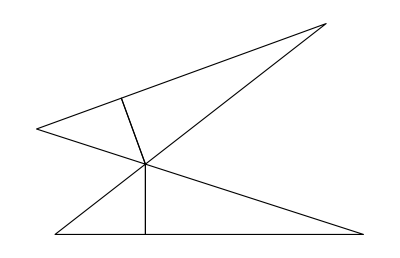

```mathematica
mesh["Wireframe"[pos]]
```

Additionally, highlight the element markers in blue:

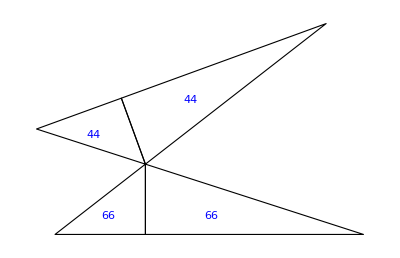

```mathematica
mesh["Wireframe"[pos,"MeshElementMarkerStyle"->Blue]]
```

Find the positions of elements that have a certain marker:

```mathematica
pos=Position[ElementMarkers[mesh["MeshElements"]],44]
```

{{1,4},{1,5},{1,6}}

Visualize just those mesh elements as a wireframe:

```mathematica
mesh["Wireframe"[pos]]
```

Directly visualize mesh elements that contain markers as a wireframe:

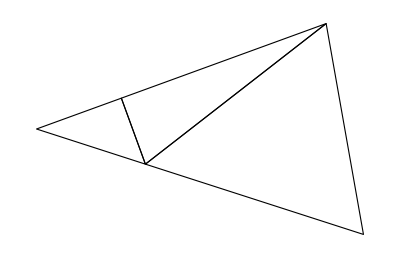

```mathematica
mesh["Wireframe"[ElementMarker==44]]
```

Visualize the boundary element mesh wireframe:

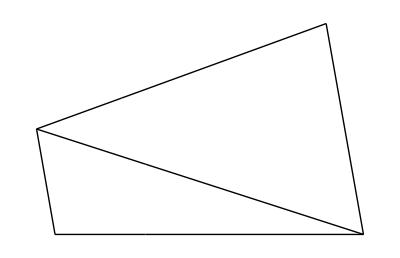

```mathematica
mesh["Wireframe"["MeshElement"->"BoundaryElements"]]
```

Visualize the boundary element mesh wireframe with the element markers in blue:

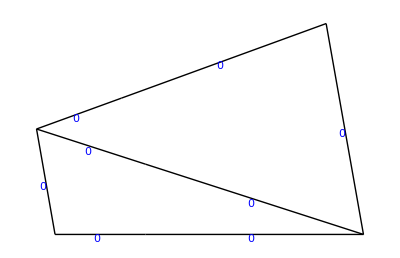

```mathematica
mesh["Wireframe"["MeshElement"->"BoundaryElements","MeshElementMarkerStyle"->Blue]]
```

Visualize the point element mesh wireframe:

```mathematica
mesh["Wireframe"["MeshElement"->"PointElements"]]
```

-Graphics-

Visualize a combination of different aspects of an element mesh:

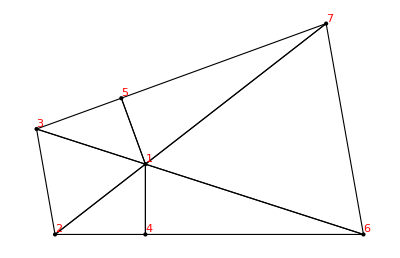

```mathematica
Show[mesh["Wireframe"],mesh["Wireframe"["MeshElement"->"PointElements","MeshElementIDStyle"->Red]]]
```

Inspect the boundary and point elements:

```mathematica
mesh["BoundaryElements"]
```

{LineElement[{{3,2},{1,3},{2,4},{4,6},{6,1},{6,7},{7,5},{5,3}}]}

```mathematica
mesh["PointElements"]
```

{PointElement[{{1},{2},{3},{4},{5},{6},{7}}]}

## Converting Images to Meshes

```mathematica
ekb = -Graphics-;
```

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
mesh = ToElementMesh[ImageMesh[ekb]]
```

ElementMesh[{{0.,302.},{0.,78.}},{TriangleElement[<1859>]}]

```mathematica
op=-Laplacian[u[x,y],{x,y}]-20
```

-20-u^(0,2)[x,y]-u^(2,0)[x,y]

```mathematica
Γ=DirichletCondition[u[x,y]==0, True]
```

DirichletCondition[u[x,y]==0,True]

```mathematica
ufun=NDSolveValue[{op==0,Γ},u,{x,y}∈mesh]
```

InterpolatingFunction[…]

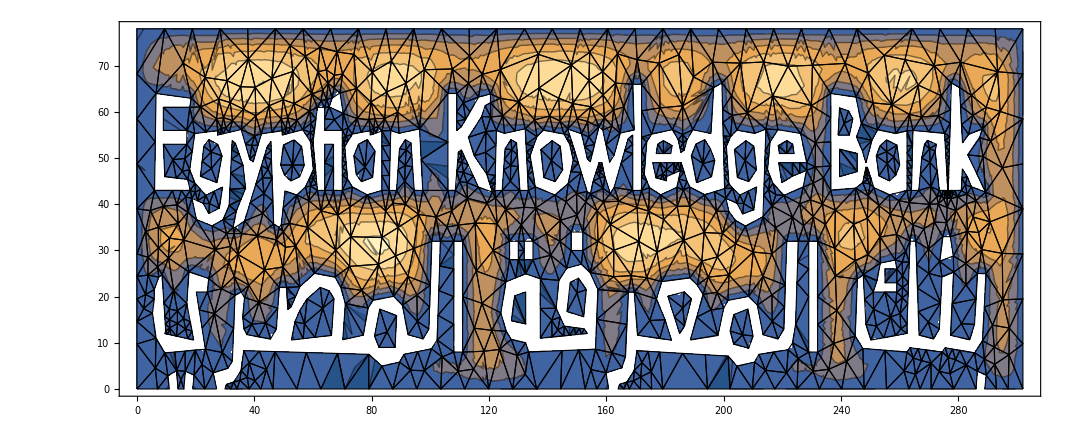

```mathematica
Show[
ContourPlot[ufun[x,y],{x,y}∈mesh,AspectRatio->Automatic],
ufun["ElementMesh"]["Wireframe"]]
```

## Three Dimensional Meshes

```mathematica
mr=BoundaryDiscretizeGraphics[ExampleData[{"Geometry3D","SpaceShuttle"}]]
```

-Graphics3D-

```mathematica
uif=NDSolveValue[{Inactive[Laplacian][u[x,y,z],{x,y,z}]==0,DirichletCondition[u[x,y,z]==1,z≤-1.3],DirichletCondition[u[x,y,z]==0,x≤-7.]},u,{x,y,z}∈mr];
```

```mathematica
Needs["NDSolve`FEM`"]
ElementMeshSurfacePlot3D[uif,Boxed->False,ViewPoint->{0,-4,2}]
```

-Graphics3D-